```mathematica
Ejemplo 1
```

# Algoritmo Genetico Ejemplo 1

## Dibuja la superficie y los valores de cada generación

```mathematica
life[e_,f_,{ax_,bx_},{ay_,by_}]:=Module[{n,ptos,graph},
		n=Length[e[[1,1]]];
		ptos=Table[Join[e[[i,1,j]],{e[[i,2,j]]}],{i,1,genera},{j,1,n}];
	ptos=Table[Map[Point,ptos[[i]]],{i,1,genera}];
		graph=Plot3D[Evaluate[f[{x,y}]],{x,ax,bx},{y,ay,by},Mesh->False,PlotPoints->25,DisplayFunction->Identity];
			Table[Show[graph,	
	Graphics3D[{PointSize[0.05],ptos[[i]]}],
ViewPoint->{1.290, -3.262, 1.850},DisplayFunction->$DisplayFunction,AspectRatio->Automatic],{i,1,genera}]
];
```

## Dibuja el mejor valor de cada Generacion

```mathematica
exhibit[matr_]:=Module[{n},
		n=Length[matr];
	ListPlot[{Table[Last[matr[[i,2]]],{i,1,n}],
				Table[matr[[i,3]],{i,1,n}]},
				Joined->True,Frame->True,PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]}]
				]
```

## Programa del Algoritmo Genetico

```mathematica
GA[Fobjetive_,{ax_,bx_},{ay_,by_},prec_,popsize_,pcross_,pmuta_,generate_]:=
	Module[{
			pop={},generacN=0,
	  newpop={},fitness={},
			notification={},
		evolution={},xsize,ysize,chromsize,xfactor,
       yfactor,finx,iniy,finy,
			meanfit,maxfit,best},
(*tamaño de c/var y factor de conversión*)
Size[{a_,b_},pre_]:=Ceiling[Log[2,(b-a)*pre]];fac[larg_,m_]:=N[larg/(2^m-1)];
		(*inicializacion poblac*)
birth[psize_,chsize_]:=
Partition[Table[Random[Integer],{chsize*psize}],chsize];
		(*decodificacion: entra chromosoma y sale el individuo*)
decode[chrom_]:=Module[{xx,yy},
				decim[gen_]:=gen.Reverse[(2^(#-1))& /@  Range[Length[gen]]];	xx= ax+decim[Take[chrom,{1,finx}]]*xfactor ;
		       yy=ay+decim[Take[chrom,{iniy,finy}]]*yfactor ; 
		Return[List[xx,yy]]
			];
		
		(*evalua un individuo de la forma apropiada
		fitForm[ind_]:=Module[{},*)
	
		          (*entra poblacion y sale lista: n mejores + sus ajustes + media geracional*)
			report[popul_,n_]:=Module[{majors,listfit,f,m,b},
					majors={decode[best]};
					listfit={maxfit};
					f=DeleteCases[fitness,maxfit];
					Do[m=Max[f];
						     b=First[Extract[popul,Position[f,m]]];
						    listfit=Join[{m},listfit];
						    majors=Join[{decode[b]},majors];
						   f=DeleteCases[f,m],
						{n-1}];
					meanfit=Plus@@fitness/popsize;
					Return[{majors,listfit,meanfit}]
				];
				(*Por el metodo "Remainder stochastic sampling with replacement"*)
	clones[popul_]:=Module [{ expected,remainder,acum,probwheel,wincopies,popaux},
		expected=fitness/meanfit ;
		popaux=Flatten[MapThread[Table[#1,{#2}]&,{popul,IntegerPart[expected]}],1];
	  probwheel=FractionalPart[ expected]/(Plus@@FractionalPart[expected]);
    acum=Rest[FoldList[Plus, 0.0, probwheel]];
    remainder=popsize-Length[popaux];
		wincopies=Table[(r=Random[]; i=1;Scan[If[#>r, Return[pop[[i]]], i++]&, acum]),
				{remainder}];
	 Flatten[List[popaux,wincopies],1]
		];
		(*entra poblac, se sortea segun pcross, los elegidos se aparean y se cruzan*)
		crossover[popnew_]:=Module[{mate,luck,children,popaux=popnew},	
		luck=Position[Table[Random[],{popsize}],r_/;r<pcross];
		If[OddQ[Length [luck]],luck=Rest[luck]];
		mate=Partition[Extract[popnew,luck],2];			
		children=Map[(j=Random[Integer,{1,(chromsize-1)}];
				List[Join[Take[#[[1]],j],Take[#[[2]],(j-chromsize)]],Join[Take[#[[2]],j],Take[#[[1]],(j-chromsize)]]])&,mate];
		children=Flatten[children,1];
		luck=Flatten[luck];
		Scan[(popaux[[luck[[#]]]]=children[[#]])& ,Range[Length[luck]]];
		Return[popaux]
		];
		(*Operador sobre los bits, y pmuta es deterministica*)
		mutation[popnew_]:=Module[{luck,tot=chromsize*popsize,popaux=popnew},
		luck=Table[Random[Integer,{1,tot}], {pmuta*tot}];
		popaux=Flatten[popaux];
		Scan[If[popaux[[#]]==0,popaux[[#]]=1,popaux[[#]]=0]&,luck];
		Return[Partition[popaux,chromsize]]		
		];		
		(* Main program *)	
      xsize=Size[{ax,bx},prec];
      ysize=Size[{ay,by},prec];
						chromsize=Plus@@{xsize,ysize};
       xfactor=fac[(bx-ax),xsize];
						yfactor=fac[(by-ay),ysize];
        finx=xsize; 
iniy=xsize+1;    finy=xsize+ysize;
		pop=birth[popsize,chromsize];
		generacN=1;
		While[generacN ≤ generate,
		Print[generacN];
	fitness=Map[Fobjetive[#]&,decode[#]&/@pop];
		maxfit=Max[fitness];
		best=First[Extract[pop,Position[fitness,maxfit]]];
         notification=report[pop,5];(*n mejores*)
			Print[notification];
		evolution=Join[evolution,{notification}];
		newpop=clones[pop];
		newpop=crossover[newpop];
		newpop=mutation[newpop];
		(*elitismo*) 
		newpop[[1]]=best;
		pop=newpop;
		generacN++;
		newpop={};
];
Return[evolution]
]
```

```mathematica
Fopt=Function[{u},-u[[1]]^2-u[[2]]^2+ 250];
 rangoX={-10,10};
 rangoY={-10 ,10};
	 precis=10^3;
psize=20;
pcro=0.25;
pmu=0.1;
genera=20;
sizeSave=5;
```

```mathematica
ev=GA[Fopt,rangoX,rangoY,precis,psize,pcro,
	pmu,genera];
```

1

{{{7.64702,-6.66677},{-1.99072,-4.36567},{1.43712,-0.995209},{-1.21799,1.69958},{1.43712,-0.995209}},{219.706,226.978,228.63,245.628,246.944},188.008}

2

{{{-5.86047,0.687582},{4.03058,-5.24888},{-5.86047,0.687582},{-3.63994,6.69973},{1.43712,-0.995209}},{240.455,240.959,241.908,246.609,246.944},206.429}

3

{{{-7.59575,0.852992},{-5.89892,0.692465},{-0.27192,-2.49123},{1.43712,-0.995209},{0.446486,0.61861}},{239.522,243.72,244.009,246.944,249.418},193.42}

4

{{{-1.50243,-1.83203},{-6.99271,0.692465},{-6.99271,0.692465},{-5.90014,2.72256},{0.446486,0.61861}},{235.772,244.182,244.386,248.994,249.418},198.925}

5

{{{-1.95471,-4.31257},{-1.95471,-4.31257},{-1.50365,-1.83203},{-5.82202,2.68349},{0.446486,0.61861}},{237.052,244.383,244.604,248.778,249.418},212.657}

6

{{{4.06476,-1.83691},{-1.50365,-6.67592},{-3.73211,2.11951},{-1.50365,-6.67592},{0.446486,0.61861}},{236.465,238.999,239.969,248.777,249.418},211.952}

7

{{{-3.63506,0.454421},{-6.99698,-0.693075},{1.2656,-0.506302},{-7.67998,4.68184},{0.446486,0.61861}},{231.948,236.474,236.58,248.142,249.418},198.614}

8

{{{0.630207,4.52498},{-6.99698,9.29991},{-1.14475,5.45701},{6.90481,-0.582598},{0.446486,0.61861}},{230.245,236.459,246.946,248.142,249.418},201.923}

9

{{{9.40306,5.45701},{3.13028,3.90118},{-6.20838,1.31321},{-2.39235,-1.52318},{0.446486,0.61861}},{241.957,244.32,246.96,248.588,249.418},213.222}

10

{{{0.755943,-8.07978},{1.22654,-5.27329},{3.00027,-7.26676},{3.00027,-7.26676},{0.446486,0.61861}},{241.526,244.937,247.528,248.121,249.418},211.357}

11

{{{4.07331,-0.184027},{2.6249,-8.68954},{0.446486,0.61861},{3.72662,-5.244},{0.446486,0.61861}},{237.441,240.251,243.071,247.042,249.418},206.298}

12

{{{0.446486,0.61861},{-3.53801,9.8114},{-3.39824,1.46519},{0.446486,0.61861},{0.446486,0.61861}},{230.706,236.305,240.31,243.974,249.418},193.087}

13

{{{4.61531,-0.116276},{-5.26536,-4.81429},{0.746788,-7.92291},{6.47816,0.531938},{0.446486,0.61861}},{220.09,226.961,228.187,228.685,249.418},187.277}

14

{{{6.78091,3.01248},{-9.53063,0.992767},{6.78091,3.01248},{-3.22489,4.80636},{0.446486,0.61861}},{220.186,223.039,228.675,228.932,249.418},181.481}

15

{{{-3.22733,4.19111},{9.61669,-5.15061},{6.7626,7.34184},{6.88772,-1.6068},{0.446486,0.61861}},{221.618,221.648,222.019,223.06,249.418},176.573}

16

{{{7.31559,-5.40513},{-8.23969,0.419019},{-7.04031,-5.53697},{0.176092,-4.43648},{0.446486,0.61861}},{207.04,220.239,230.287,244.526,249.418},170.349}

17

{{{-8.23969,2.99478},{2.67617,-4.91989},{7.257,4.75143},{-9.8236,-4.52437},{0.446486,0.61861}},{218.633,221.618,226.053,247.052,249.418},186.431}

18

{{{0.177313,5.54735},{0.276193,5.61632},{0.446486,0.61861},{5.98804,-9.44151},{0.446486,0.61861}},{234.84,242.93,247.052,247.119,249.418},204.36}

19

{{{3.38176,-2.47963},{2.92825,-6.79678},{3.38176,-2.08594},{0.446486,0.61861},{0.207831,0.497757}},{242.883,245.471,246.695,249.418,249.709},206.614}

20

{{{-3.58989,6.53615},{-0.101016,-0.363475},{0.401929,-2.62001},{0.207831,0.497757},{-0.101016,-0.363475}},{237.624,242.974,246.86,249.709,249.858},204.176}

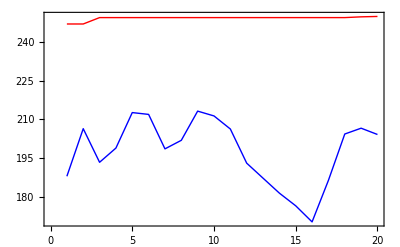

```mathematica
exhibit[ev]
```

```mathematica
life[ev,Fopt,rangoX,rangoY]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(* Es una función sencilla cuyo maximo ocurre en (0,0) 
El criterio de la segunda derivada y los algoritmos geneticos
coinciden en los resultados *)
```